```mathematica
collatz[n_Integer/;n∈]:=Piecewise[{{n/2, EvenQ[n]}, {3n+1, OddQ[n]}}]
```

```mathematica
Table[collatz[i],{i,1,20,1}]
```

{4,1,10,2,16,3,22,4,28,5,34,6,40,7,46,8,52,9,58,10}

```mathematica
collatz[-1]
```

collatz[-1]

```mathematica
Nest[collatz,10,1]
```

5

```mathematica
NestList[collatz,7,10]
```

{7,22,11,34,17,52,26,13,40,20,10}

```mathematica
NestList[collatz,7,20]
```

{7,22,11,34,17,52,26,13,40,20,10,5,16,8,4,2,1,4,2,1,4}

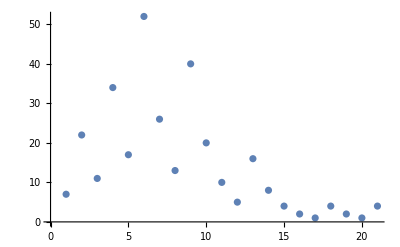

```mathematica
ListPlot@NestList[collatz,7,20]
```

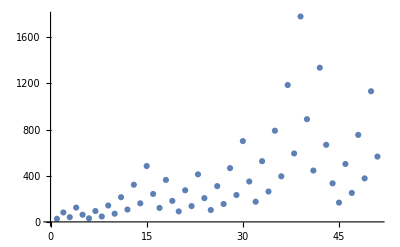

```mathematica
ListPlot@NestList[collatz,27,50]
```

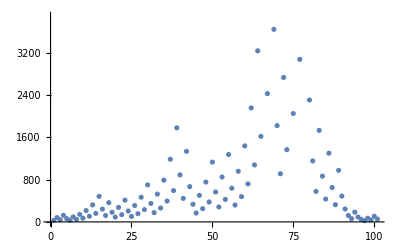

```mathematica
ListPlot@NestList[collatz,27,100]
```

```mathematica
recurse[n_Integer/;n∈]:=Piecewise[{{□, □}, {□, □}}]
```

```mathematica
count[n_Integer/;n∈]:=Piecewise[{{count[n]=0, n==1}, {count[n]=count[collatz[n]]+1, n>1}}]
```

```mathematica
count[1]
```

0

```mathematica
count[2]
```

1

```mathematica
count[3]
```

7

```mathematica
count[27]
```

111

```mathematica
ccol[n_Integer/;EvenQ[n]]:=n/2
```

```mathematica
Map[ccol,{1,2,3.4,-32,3+3I}]
```

{ccol[1],1,ccol[3.4],-16,ccol[3+3 ⅈ]}

```mathematica
Map[ccol,{1,2,3.4,-32,3+3I,4}]
```

{ccol[1],1,ccol[3.4],-16,ccol[3+3 ⅈ],2}

```mathematica
ccol[n_Integer/;OddQ[n]]:=3n+1
```

```mathematica
Map[ccol,{1,2,3.4,-32,3+3I,4,5}]
```

{4,1,ccol[3.4],-16,ccol[3+3 ⅈ],2,16}

```mathematica
count[]
```

count[]